```mathematica
(* функции взаимодействия с программой на C++ *)
ReadData[filename_] := Module[{data,T,E ,C ,M ,Mafm,MafmSum,χ,χafm,χafmLines,i,j, count,Js,NumberPar},
data=ReadList[filename,Word,WordSeparators->{";"}];
NumberPar=9;(*Количество наблюдаемых*)
Js=ToExpression[data[[1]]];
count = (Length[data]-1)/NumberPar; (* количество строк *)
(*E = Table[{},count*countJs];
M = Table[{},count*countJs];
Mafm = Table[{},count*countJs];
MafmSum = Table[{},count*countJs];
C = Table[{},count*countJs];
χ= Table[{},count*countJs];
χafm= Table[{},count*countJs];
χafmLines= Table[{},count*countJs];*)
E = Table[{},count];
M = Table[{},count];
Mafm = Table[{},count];
MafmSum = Table[{},count];
C = Table[{},count];
χ= Table[{},count];
χafm= Table[{},count];
χafmLines= Table[{},count];
For[i=0,i<count,i++,
(*T = ToExpression[data[[NumberPar*i+1+3+j+j*NumberPar*count+1]]];
E[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+2+3+j+j*NumberPar*count+1]]]};
M[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+3+3+j+j*NumberPar*count+1]]]};
Mafm[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+4+3+j+j*NumberPar*count+1]]]};
MafmSum[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+5+3+j+j*NumberPar*count+1]]]};
C[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+6+3+j+j*NumberPar*count+1]]]};
χ[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+7+3+j+j*NumberPar*count+1]]]};
χafm[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+8+3+j+j*NumberPar*count+1]]]};
χafmLines[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+9+3+j+j*NumberPar*count+1]]]};*)
T = ToExpression[data[[NumberPar*i+1+1]]];
E[[i+1]] = {T,ToExpression[data[[NumberPar*i+2+1]]]};
M[[i+1]] = {T,ToExpression[data[[NumberPar*i+3+1]]]};
Mafm[[i+1]] = {T,ToExpression[data[[NumberPar*i+4+1]]]};
MafmSum[[i+1]] = {T,ToExpression[data[[NumberPar*i+5+1]]]};
C[[i+1]] = {T,ToExpression[data[[NumberPar*i+6+1]]]};
χ[[i+1]] = {T,ToExpression[data[[NumberPar*i+7+1]]]};
χafm[[i+1]] = {T,ToExpression[data[[NumberPar*i+8+1]]]};
χafmLines[[i+1]] = {T,ToExpression[data[[NumberPar*i+9+1]]]};
];

{E,M,Mafm,MafmSum,C,χ,χafm,χafmLines,Js}
]
```

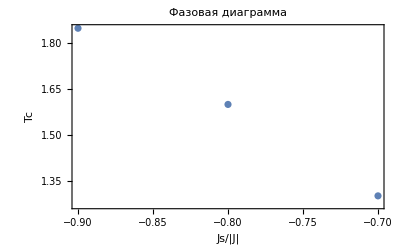

```mathematica
(* чтение результатов из тестового файла *)
(*filename = SystemDialogInput["FileOpen", NotebookDirectory[]];
{cppE,cppM,cppMafm,cppMafmSum,cppC,cppChi,cppChiafm,cppChiafmLines,countJs,Js,dJs,count} = ReadData[filename];*)


files=SystemDialogInput["FileOpen", NotebookDirectory[]];
If[Length[files]==0,files={files}];
cppE =cppM = cppMafm =cppMafmSum= cppC = cppChi = cppChiafm =cppChiafmLines=Js= Table[0,Length[files]];
For[k = 1, k ≤Length[files],k++,
{cppE[[k]],cppM[[k]],cppMafm[[k]],cppMafmSum[[k]],cppC[[k]],cppChi[[k]],cppChiafm[[k]],cppChiafmLines[[k]],Js[[k]]} = ReadData[files[[Length[files]-k+1]]];
];
(*cppEJ[j_]:=Table[cppE[[i+(j-1)*count]],{i,1,count}];
cppMJ[j_]:=Table[cppM[[i+(j-1)*count]],{i,1,count}];
cppMafmJ[j_]:=Table[cppMafm[[i+(j-1)*count]],{i,1,count}];
cppMafmSumJ[j_]:=Table[cppMafmSum[[i+(j-1)*count]],{i,1,count}];
cppCJ[j_]:=Table[cppC[[i+(j-1)*count]],{i,1,count}];
cppChiJ[j_]:=Table[cppChi[[i+(j-1)*count]],{i,1,count}];
cppChiafmJ[j_]:=Table[cppChiafm[[i+(j-1)*count]],{i,1,count}];
cppChiafmLinesJ[j_]:=Table[cppChiafmLines[[i+(j-1)*count]],{i,1,count}];*)
count=Length[cppE [[1]]];
maxValue=Table[{},Length[files]];
For [p=1,p<=Length[files],p++,
valueMaxC=Max[Table[cppC[[p]][[j]][[2]],{j,1,count}]];
For[k=1,k≤count,k++,
If[cppC[[p]][[k]][[2]]==valueMaxC,
maxValue[[p]]={Js[[p]],cppC[[p]][[k]][[1]]};
];
];
];

ListPlot[maxValue,Frame->True,FrameLabel->{"Js/|J|","Tc"},PlotRange->All,PlotLabel->"Фазовая диаграмма"]

(*conterMaximum=Table[0,countJs];
For[i=1,i<=countJs,i++,
countMax=0;
For[j=2,j<count,j++,
botC=cppCJ[i][[j-1]][[2]];
midC=cppCJ[i][[j]][[2]];
topC=cppCJ[i][[j+1]][[2]];
If[(botC<midC),If[(midC>topC),countMax++]];

];
conterMaximum[[i]]=countMax;
];
maximums[i_]:=Table[0,i];
For[i=1,i<=countJs,i++,
conterLocal=0;
maxI=maximums[conterMaximum[[i]]];
For[j=2,j<count,j++,

botC=cppCJ[i][[j-1]][[2]];
midC=cppCJ[i][[j]][[2]];
topC=cppCJ[i][[j+1]][[2]];
If[(botC<midC),If[(midC>topC),conterLocal++;maxI[[conterLocal]]={Js+dJs*(i-1),cppCJ[i][[j]][[1]]}]];
];
maxValue[[i]]=maxI;
];


ListPlot[maxValue,Frame->True,FrameLabel->{"Js/|J|","Tc"},PlotRange->All,PlotLabel->"Фазовая диаграмма"]*)



Manipulate[ListPlot[cppE[[j]],Frame->True,FrameLabel->{"T/J","E"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
Manipulate[ListPlot[cppC[[j]],Frame->True,FrameLabel->{"T/J","C"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
Manipulate[ListPlot[{cppM[[j]],cppMafm[[j]]},Frame->True,FrameLabel->{"T/J","M,Mafm"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
Manipulate[ListPlot[cppMafmSum[[j]],Frame->True,FrameLabel->{"T/J","MafmSum"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
Manipulate[ListPlot[cppChi[[j]],Frame->True,FrameLabel->{"T/J","χ"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
Manipulate[ListPlot[cppChiafm[[j]],Frame->True,FrameLabel->{"T/J","χafm"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
Manipulate[ListPlot[cppChiafmLines[[j]],Frame->True,FrameLabel->{"T/J","χafmLines"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js[[j]]])],{j,1,Length[files],1}]
```

```mathematica
(* чтение нескольких файлов *)
files= SystemDialogInput["FileOpen", NotebookDirectory[]];
cppE = cppM = cppMafm = cppC = cppChi = cppChiafm = Table[0,Length[files]];
For[k = 1, k ≤Length[files],k++,
{cppE[[k]],cppM[[k]],cppMafm[[k]],cppC[[k]],cppChi[[k]],cppChiafm[[k]]} = ReadData[files[[k]]];
]
ListPlot[cppE,Frame->True,FrameLabel->{"T/J","E"},PlotRange->All]
ListPlot[cppM,Frame->True,FrameLabel->{"T/J","M"},PlotRange->All]
ListPlot[cppMafm,Frame->True,FrameLabel->{"T/J","Mafm"},PlotRange->All]
ListPlot[cppC,Frame->True,FrameLabel->{"T/J","C"},PlotRange->All]
ListPlot[cppChi,Frame->True,FrameLabel->{"T/J","χ"},PlotRange->All]
ListPlot[cppChiafm,Frame->True,FrameLabel->{"T/J","χ"},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»